```mathematica
BinarySum[v_,b_]:=FullSimplify[Sum[v,{b,0,3}],_∈Integers];
FoldedSum[v_,vars_]:=FullSimplify[Fold[BinarySum,v,vars],_∈Integers];
```

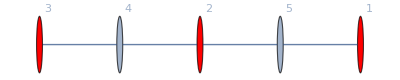

(1+(-1)^b[4])^2

8

```mathematica
CharacteristicSummand[G_,A_]:=Module[{P},
P=(-1)^Sum[b[n]*Sum[b[DeleteCases[VertexList[NeighborhoodGraph[G,n,1]],n][[m]]],{m,Length[DeleteCases[VertexList[NeighborhoodGraph[G,n,1]],n]]}],{n,Length[A]}];
FoldedSum[P,Table[b[n],{n,1,Length[A]}]]
]

Renyi[G_,A_]:=Module[
{NumVertices,P},
NumVertices=VertexCount[G];
P=CharacteristicSummand[G,A];
Print[P];
S=-Log2[FoldedSum[P,Table[b[n],{n,Last[A]+1,NumVertices}]]/2^(2*NumVertices)]
];

A={1,2,3};
NumVertices=5;
Vertices=Table[If[MemberQ[A,n],Style[n,Red],n],{n,1,NumVertices}];
G=Graph[Vertices,{1<->5,5<->2,2<->4,3<->4},VertexLabels->"Name"]
Sum[CharacteristicSummand[G,A]/8,{b[5],0,3}]/4
Sum[%,{b[4],0,3}]
```

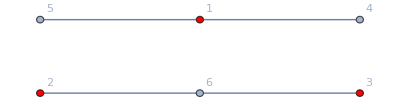

(1+(-1)^(b[4]+b[5])) (1+(-1)^b[6])^2

8 (1+(-1)^(b[4]+b[5]))

16 (1+(-1)^b[6])^2

```mathematica
A={1,2,3};
NumVertices=6;
Vertices=Table[If[MemberQ[A,n],Style[n,Red],n],{n,1,NumVertices}];
G=Graph[Vertices,{1<->4,1<->5,2<->6,3<->6},VertexLabels->"Name"]
Ch=CharacteristicSummand[G,A]/8
Sum[Ch,{b[6],0,3}]
Sum[Ch,{b[4],0,3},{b[5],0,3}]
```

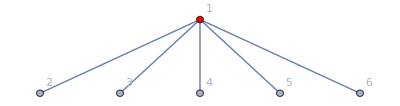

10

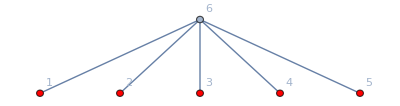

6

```mathematica
NumVertices=6;
A={1};
Vertices=Table[If[MemberQ[A,n],Style[n,Red],n],{n,1,NumVertices}];
G=Graph[Vertices,Table[1<->n,{n,2,NumVertices}],VertexLabels->"Name"]
Log2@FoldedSum[CharacteristicSummand[G,A]/2,Table[b[n],{n,1,NumVertices-1}]]

A=Table[n,{n,1,NumVertices-1}];
Vertices=Table[If[MemberQ[A,n],Style[n,Red],n],{n,1,NumVertices}];
G=Graph[Vertices,Table[NumVertices<->n,{n,1,NumVertices-1}],VertexLabels->"Name"]
Log2@FoldedSum[CharacteristicSummand[G,A]/2^(NumVertices-1),{b[NumVertices]}]
```

```mathematica
PartialLoopWithEdges[n_,nmax_,vars_]:=Product[1+(-1)^(x[m]+x[Mod[m+1,n]]+vars[[m+1]]),{m,0,nmax-1}];
LoopWithEdges[n_,vars_]:=PartialLoopWithEdges[n,n,vars];
PartialLoop[n_,nmax_]:=PartialLoopWithEdges[n,nmax,Table[0,{m,0,nmax-1}]];
Loop[n_]:=LoopWithEdges[n,Table[0,{m,0,n-1}]];

PartialLoop[4,3]
PartialLoopWithEdges[4,3,{0,0,0}]
```

(1+(-1)^(x[0]+x[1])) (1+(-1)^(x[1]+x[2])) (1+(-1)^(x[2]+x[3]))

(1+(-1)^(x[0]+x[1])) (1+(-1)^(x[1]+x[2])) (1+(-1)^(x[2]+x[3]))

```mathematica
FullSimplify@Sum[(1+(-1)^x)*(1+(-1)^(x+y))*(1+(-1)^y),{x,0,3}]
FullSimplify@Sum[(1+(-1)^x)*(1+(-1)^(x+y))*(1+(-1)^y)/4,{x,0,3},{y,0,3}]
```

4 (1+(-1)^y)^2

8